```mathematica
EstimatedDistribution[{0,-1,0,0,1,0,1,1},f[t]]
```

FindDistributionParameters::vloc: 无法将变量 Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t] 局部化，因此它可以被赋值为数值变量.

FindDistributionParameters[{0,-1,0,0,1,0,1,1},ProbabilityDistribution[Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t],{x,-1,1,1}]]

```mathematica
(*极大似然*)
FindDistributionParameters[{1.5,1.8,2.2,2.5,2.8,1.2},UniformDistribution[{1,1+a}]]
```

{a→1.8}

```mathematica
(*矩估计*)
FindDistributionParameters[{1.5,1.8,2.2,2.5,2.8,1.2},UniformDistribution[{1,1+a}],ParameterEstimator->"MethodOfMoments"]
```

{a→2.}

```mathematica
f[t_]=ProbabilityDistribution[Which[
x==-1,t (1-t),
x==0,(1-t)^2,
x==1,t 
],{x}]
```

ProbabilityDistribution[Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t],{x}]

```mathematica
f[t_]=ProbabilityDistribution[Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t],{x,-1,1,1}]
```

ProbabilityDistribution[Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t],{x,-1,1,1}]

```mathematica
PDF[dis,x]
```

Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t]

```mathematica
-t(1-t)+t//FullSimplify
```

t^2

```mathematica
f[x_]=Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t]
```

Which[x==-1,t (1-t),x==0,(1-t)^2,x==1,t]

```mathematica
f/@{0,-1,0,0,1,0,1,1}
```

```mathematica
{(1-t)^2,(1-t) t,(1-t)^2,(1-t)^2,t,(1-t)^2,t,t}//Times@@#&
```

```mathematica
(1-t)^9 t^4//Maximize[{#,0≤t<=1},t]&
```

{99179645184/302875106592253,{t→4/13}}

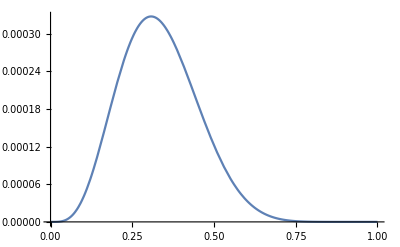

```mathematica
(1-t)^9 t^4//Plot[#,{t,0,1}]&
```

```mathematica
4/13.
```

0.307692

```mathematica
1-(1-t)^2/.t->4/13//N
```

0.52071

```mathematica
t(1-t)+(1-t)^2+t//Simplify
```

1

```mathematica
Reduce[(2 *3)/Sqrt[n]*1.96≤1,n]
```

Reduce::ratnz: Reduce 无法求解具有不精确系数的系统. 答案是通过求解相应的精确系统并且将结果数值化处理得到的.

n≥138.298

```mathematica
Solve[11.76/(√n)≤1&&n∈Integers,{n}]
```

Solve::nsmet: 无法利用 Solve 现有的方法求解该系统.

Solve::inex: Solve 无法求解具有不精确系数的系统，或是通过将系统中出现的不精确数直接合理化处理得到的系统. 由于 Solve 所用的许多方法需要精确输入，为 Solve 提供一个精确版本的系统可能会有帮助.

Solve::cpow: Solve 无法证明只包含实数变量和参数的表达式的根是实数值. 如果您只对输入中包含的所有根是实数的情况下的解感兴趣，请使用域参数为 Reals 的 Solve.

Solve[11.76/(√n)≤1&&n∈ℤ,{n}]

```mathematica
Abs@InverseCDF[NormalDistribution[],0.975]
```

1.95996